```mathematica
(* TECHNOLOGY PARAMETER FITTING *)

(* Clear everything *)
ClearAll["Global`*"]

(* Parameters: modify for each technology *)
fs=10^3;
techAParams={ρ->0.3*10^-6,Lmax->4*10^-9,wmax->50*10^-9,LT->1*10^-9,w0->0.5*10^-9,Rpar->2000,VT->0.4,I0->5*10^14,Ea1->1.2,Ea2->1.2,kT->0.026,gmax->240*10^-6,γ->10^6,w1->1*10^-10,w2->1*10^-9};
techBParams={ρ->0.3*10^-6,Lmax->3*10^-9,wmax->50*10^-9,LT->0.5*10^-9,w0->0.5*10^-9,Rpar->5000,VT->0.4,I0->5*10^14,Ea1->1.2,Ea2->1.2,kT->0.026,gmax->128*10^-6,γ->10^6,w1->1*10^-10,w2->1*10^-9};
techCParams={ρ->8*10^-6,Lmax->8*10^-9,LT->0.4*10^-9,w0->0.5*10^-9,Rpar->10000,VT->0.4,I0->5*10^13,Ea1->1.2,Ea2->1.2,kT->0.026,gmax->40*10^-6,γ->10^12,w1->1*10^-10,w2->1*10^-9,n->10^3};
subs=techCParams;

(* Functions for conductance as a function of length and area in Stages 1 and 2 *)
g[A_,L_]:=(VT/(I0 A ⅇ^(-(Lmax-L)/LT))+(ρ L)/A+Rpar)^-1
gs1[L_]:=g[A0,L]
gs2[A_]:=g[A,Lmax]

(* Maximum conductance, length, area *)
A0=(π w0^2)/4
gtr=g[A0,Lmax]
gmax=gmax/.subs
Lmax=Lmax/.subs
Amax=InverseFunction[gs2][gmax]/.subs
w0=w0/.subs
A0/.subs

(* Show value for transition point between Stages 1 and 2 for conductance and volume *)
gtr*10^6/.subs

(4 VT)/(I0 π w0^2)/.subs
(4 Lmax ρ)/(π w0^2)/.subs
```

(π w0^2)/4

1/(Rpar+(4 VT)/(I0 π w0^2)+(4 Lmax ρ)/(π w0^2))

1/25000

1/125000000

4.8×10^-18

5.×10^-10

1.9635×10^-19

2.65468

40743.7

325949.

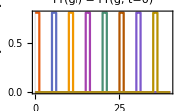

```mathematica
(* GENERATE INITIAL CONDUCTANCE DISTRIBUTIONS *)

(* Initial distribution settings *)
nranges=8;
gwidth=gmax/32;
gmeans=Range[gwidth/2,gmax,gmax/nranges];

(* Initial conductance distribution *)
gidists=Table[UniformDistribution[{gval-gwidth/2,gval+ gwidth/2}],{gval,gmeans}];
(*gidists=Table[NormalDistribution[gval,gwidth],{gval,gmeans}];*)
gidistpdfs=Table[PDF[gidist,g],{gidist,gidists}];
scaled=gidistpdfs/10^6/.{g->x/10^6};
Plot[scaled,{x,0,gmax*10^6},PlotRange->All,PlotLabel->"Pr(g_i) = Pr(g, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]
```

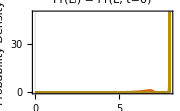

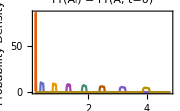

```mathematica
(* TRANSLATE CONDUCTANCE DISTRIBUTIONS TO AREA/LENGTH DISTRIBUTIONS *)

(* Use interpolation for inverse function, then sample and generate KDE *)
npts=1000;
nsamps=1000;

Off[General::munfl]
LDist[samps_]:=If[Variance[samps]>0,KernelMixtureDistribution[samps,MaxMixtureKernels->All],NormalDistribution[Mean[samps]-5*Lmax/npts,Lmax/npts]]
ADist[samps_]:=If[Variance[samps]>0,KernelMixtureDistribution[samps,MaxMixtureKernels->All],NormalDistribution[Mean[samps]+5*(Amax-A0)/npts,(Amax-A0)/npts]]

(* Length as function of conductance *)
gs1invpts=Table[{gs1[L]/.subs,L},{L,0,Lmax,Lmax/npts}];
PrependTo[gs1invpts,{0,0}];
AppendTo[gs1invpts,{gmax,Lmax}];
gs1inv=Interpolation[gs1invpts,InterpolationOrder->1]; 
(*Plot[gs1inv[g/10^6],{g,0,gmax*10^6},PlotRange->All]*)

(* Area as function of conductance *)
gs2invpts=Table[{gs2[A]/.subs,A},{A,A0,Amax,(Amax-A0)/npts}];
PrependTo[gs2invpts,{0,A0}];
gs2inv=Interpolation[gs2invpts,InterpolationOrder->1]; 

(* Length distribution *)
Lidists=Table[TransformedDistribution[gs1inv[g],g\[Distributed]gidist],{gidist,gidists}];
Lisamps=Table[RandomVariate[Lidist,nsamps],{Lidist,Lidists}];
LidistKDEs=Table[LDist[Lisamp],{Lisamp,Lisamps}];
LidistKDEpdfs=Table[PDF[LidistKDE,L],{LidistKDE,LidistKDEs}];
scaled=LidistKDEpdfs/10^9/.{L->x/10^9};
Plot[scaled,{x,0,Lmax*10^9},PlotRange->All,PlotLabel->"Pr(L_i) = Pr(L, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Initial Length (nm)",None}}]

(* Area distribution *)
Aidists=Table[TransformedDistribution[gs2inv[g],g\[Distributed]gidist],{gidist,gidists}];
Aisamps=Table[RandomVariate[Aidist,nsamps],{Aidist,Aidists}];
AidistKDEs=Table[ADist[Aisamp],{Aisamp,Aisamps}];
AidistKDEpdfs=Table[PDF[AidistKDE,A],{AidistKDE,AidistKDEs}];
scaled=AidistKDEpdfs/10^18/.{A->x/10^18};
Plot[scaled,{x,A0*10^18,Amax*10^18},PlotRange->All,PlotLabel->"Pr(A_i) = Pr(A, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Initial Area (nm^2)",None}}]
```

1800

(1.83388×10^-17 n^2)/((-Ea1+Ea2)/kT+(-w1+w2) γ)

-(5.09412×10^-21 kT n^2)/(Ea1-1. Ea2+kT (w1-1. w2) γ)

5.66014×10^-18

1/100000000000000000000000

(1.10472×10^-38 n^2)/((-Ea1+Ea2)/kT+(-w1+w2) γ)

-(3.06866×10^-42 kT n^2)/(Ea1-1. Ea2+kT (w1-1. w2) γ)

3.40963×10^-39

1/25000000000000000000000000000000000000000

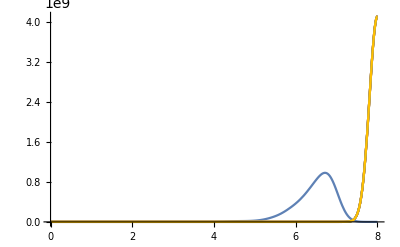

-Graphics-

```mathematica
(* SOLVE FOR FINAL LENGTH/AREA DISTRIBUTIONS *)

(* Mesh points setting *)
meshpts=1000;

(* Final time to solve for *)
tf=30*60

(* Compute constants *)
varL=((n w0^3)/A0 )^2(π Log[fs tf])/((Ea2 - Ea1)/kT + γ(w2-w1))
DiffL=Simplify[PowerExpand[varL/(2tf)]]
N[DiffL/.subs]
DiffL=10^-23

varA=((n w0^3)/Lmax )^2(π Log[fs tf])/((Ea2 - Ea1)/kT + γ(w2-w1))
DiffA=Simplify[PowerExpand[varA/(2tf)]]
N[DiffA/.subs]
DiffA=4*10^-41

(* Solve diffusion equation for length with initial/boundary conditions *)
method={"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->Lmax/meshpts}}}};
heqn=D[p[L,t],t]-D[DiffL p[L,t],{L,2}]==NeumannValue[0,L==0]+NeumannValue[0,L==Lmax];
ics=Table[p[L,0]==icfn,{icfn,LidistKDEpdfs}];
Lfpdfs=p[L,tf]/.Table[NDSolve[{heqn/.subs,ic},p[L,tf],{L,0,Lmax},{t,0,tf},InterpolationOrder->All,Method->method],{ic,ics}];
Plot[Lfpdfs,{L,0,Lmax},PlotRange->All]

(* Solve diffusion equation for area with initial/boundary conditions *)
method={"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->(Amax-A0)/meshpts}}}};
heqn=D[p[A,t],t]-D[DiffA p[A,t],{A,2}]==NeumannValue[0,A==A0]+NeumannValue[0,A==Amax];
ics=Table[p[A,0]==icfn,{icfn,AidistKDEpdfs}];
Afpdfs=p[A,tf]/.Table[NDSolve[{heqn/.subs,ic},p[A,tf],{A,A0,Amax},{t,0,tf},InterpolationOrder->All,Method->method],{ic,ics}];
Plot[Afpdfs,{A,A0,Amax},PlotRange->All]
```

```mathematica
(* TRANSLATE LENGTH/AREA DISTRIBUTIONS BACK TO CONDUCTANCE DISTRIBUTIONS *)
npts=1000;
Table[NIntegrate[Abs[Afpdf[[1]]],{A,A0,Amax},MaxRecursion->15],{Afpdf,Afpdfs}]
Table[NIntegrate[Abs[Lfpdf[[1]]],{L,0,Lmax},MaxRecursion->15],{Lfpdf,Lfpdfs}]
wfdists=Table[ProbabilityDistribution[Abs[Afpdf[[1]]],{A,A0,Amax},Method->"Normalize"],{Afpdf,Afpdfs}];
Lfdists=Table[ProbabilityDistribution[Abs[Lfpdf[[1]]],{L,0,Lmax},Method->"Normalize"],{Lfpdf,Lfpdfs}];
gfdists=MapThread[TransformedDistribution[g[A,L],{A\[Distributed]#1,L\[Distributed]#2}]&,{wfdists,Lfdists}]
```

{1.,1.,1.,1.,1.,1.,1.,1.}

{1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999}

{TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 4.8 10   }, {0., 1800.}}, <>][x,1800]],{x,1.9635×10^-19,4.8×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1800.}}, <>][x,1800]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 4.8 10   }, {0., 1800.}}, <>][x,1800]],{x,1.9635×10^-19,4.8×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1800.}}, <>][x,1800]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 4.8 10   }, {0., 1800.}}, <>][x,1800]],{x,1.9635×10^-19,4.8×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1800.}}, <>][x,1800]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 4.8 10   }, {0., 1800.}}, <>][x,1800]],{x,1.9635×10^-19,4.8×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1800.}}, <>][x,1800]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 4.8 10   }, {0., 1800.}}, <>][x,1800]],{x,1.9635×10^-19,4.8×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1800.}}, <>][x,1800]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 4.8 10   }, {0., 1800.}}, <>][x,1800]],{x,1.9635×10^-19,4.8×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1800.}}, <>][x,1800]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 4.8 10   }, {0., 1800.}}, <>][x,1800]],{x,1.9635×10^-19,4.8×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1800.}}, <>][x,1800]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 4.8 10   }, {0., 1800.}}, <>][x,1800]],{x,1.9635×10^-19,4.8×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1800.}}, <>][x,1800]],{x,0,1/125000000}]}]}

```mathematica
(* SAMPLE FINAL CONDUCTANCE DISTRIBUTIONS AND CREATE PDF *)
nsamps=1000;
gfsamps=Table[RandomVariate[gfdist/.subs,nsamps],{gfdist,gfdists}] ;
gfdistKDEs=Table[SmoothKernelDistribution[gfsamp,MaxMixtureKernels->All],{gfsamp,gfsamps}];
gfdistKDEpdfs=Table[PDF[gfdistKDE,g],{gfdistKDE,gfdistKDEs}];
data=Transpose[{gfdistKDEpdfs,gidistpdfs}];
```

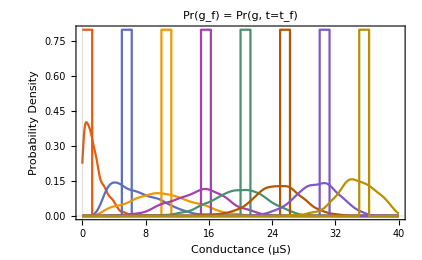

```mathematica
(* PLOT FINAL CONDUCTANCE DISTRIBUTIONS *)

(* Final conductance distributions *)
scaled=Transpose[{gfdistKDEpdfs,gidistpdfs}]/10^6/.{g->x/10^6};
Plot[scaled,{x,0,gmax*10^6},PlotRange->All,PlotLabel->"Pr(g_f) = Pr(g, t=t_f)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]
```